{0→0,1→16,2→0,3→0,4→208,5→240,6→144,7→128,8→0,9→144,10→0,11→0,12→0,13→176,14→0,15→0,16→1,17→17,18→1,19→1,20→209,21→241,22→145,23→129,24→1,25→145,26→1,27→1,28→1,29→177,30→1,31→1,32→0,33→16,34→0,35→0,36→208,37→240,38→144,39→128,40→0,41→144,42→0,43→0,44→0,45→176,46→0,47→0,48→0,49→16,50→0,51→0,52→208,53→240,54→144,55→128,56→0,57→144,58→0,59→0,60→0,61→176,62→0,63→0,64→11,65→27,66→11,67→11,68→219,69→251,70→155,71→139,72→11,73→155,74→11,75→11,76→11,77→187,78→11,79→11,80→15,81→31,82→15,83→15,84→223,85→255,86→159,87→143,88→15,89→159,90→15,91→15,92→15,93→191,94→15,95→15,96→9,97→25,98→9,99→9,100→217,101→249,102→153,103→137,104→9,105→153,106→9,107→9,108→9,109→185,110→9,111→9,112→8,113→24,114→8,115→8,116→216,117→248,118→152,119→136,120→8,121→152,122→8,123→8,124→8,125→184,126→8,127→8,128→0,129→16,130→0,131→0,132→208,133→240,134→144,135→128,136→0,137→144,138→0,139→0,140→0,141→176,142→0,143→0,144→9,145→25,146→9,147→9,148→217,149→249,150→153,151→137,152→9,153→153,154→9,155→9,156→9,157→185,158→9,159→9,160→0,161→16,162→0,163→0,164→208,165→240,166→144,167→128,168→0,169→144,170→0,171→0,172→0,173→176,174→0,175→0,176→0,177→16,178→0,179→0,180→208,181→240,182→144,183→128,184→0,185→144,186→0,187→0,188→0,189→176,190→0,191→0,192→0,193→16,194→0,195→0,196→208,197→240,198→144,199→128,200→0,201→144,202→0,203→0,204→0,205→176,206→0,207→0,208→13,209→29,210→13,211→13,212→221,213→253,214→157,215→141,216→13,217→157,218→13,219→13,220→13,221→189,222→13,223→13,224→0,225→16,226→0,227→0,228→208,229→240,230→144,231→128,232→0,233→144,234→0,235→0,236→0,237→176,238→0,239→0,240→0,241→16,242→0,243→0,244→208,245→240,246→144,247→128,248→0,249→144,250→0,251→0,252→0,253→176,254→0,255→0}

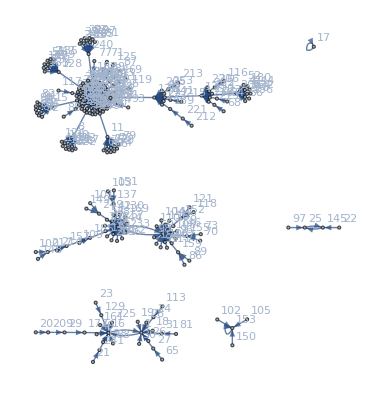

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/QGraphs/10000.png

```mathematica
weights = Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/new_file.csv"];

edges = {};
Do[Do[If[weights[[i]][[j]]==Max[weights[[i]]],AppendTo[edges,i-1->j-1]],{j,1,256}],{i,1,256}]; 
edges
graph = Graph[edges,ImageSize->Full,VertexLabels->Automatic]

Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/QGraphs/10000.png",graph]
```